```mathematica
Fij2D[q1_,q2_,q3_]:={{q2,q3},{q2^2/q1+1/2*q1^2,q2*q3/q1},{q2*q3/q1,q3^2/q1+1/2*q1^2}}
```

```mathematica
Fijnj[q1_,q2_,q3_,n1_,n2_]:=Dot[Fij2D[q1,q2,q3],{n1,n2}]
```

```mathematica
gradFijqk[q1_,q2_,q3_]=Grad[Fij2D[q1,q2,q3],{q1,q2,q3}]
```

{{{0,1,0},{0,0,1}},{{q1-q2^2/q1^2,(2 q2)/q1,0},{-(q2 q3)/q1^2,q3/q1,q2/q1}},{{-(q2 q3)/q1^2,q3/q1,q2/q1},{q1-q3^2/q1^2,0,(2 q3)/q1}}}

```mathematica
FqDotN2D[q1_,q2_,q3_,n1_,n2_]:={{0,1,0},{-q2^2/q1^2+q1,2*q2/q1,0},{-q2*q3/q1^2,q3/q1,q2/q1}}*n1+ {{0,0,1},{-q2*q3/q1^2,q3/q1,q2/q1},{-q3^2/q1^2+q1,0,2*q3/q1}}*n2
```

```mathematica
gradFqDotn[q1_,q2_,q3_,n1_,n2_]=Grad[Fijnj[q1,q2,q3,n1,n2],{q1,q2,q3}]
```

{{0,n1,n2},{n1 (q1-q2^2/q1^2)-(n2 q2 q3)/q1^2,(2 n1 q2)/q1+(n2 q3)/q1,(n2 q2)/q1},{-(n1 q2 q3)/q1^2+n2 (q1-q3^2/q1^2),(n1 q3)/q1,(n1 q2)/q1+(2 n2 q3)/q1}}

```mathematica
Eigenvalues[FqDotN2D[q1,q2,q3,n1,n2]]
```

{(n1 q2+n2 q3)/q1,(-√(n1^2 q1^5+n2^2 q1^5)+n1 q1 q2+n2 q1 q3)/q1^2,(√(n1^2 q1^5+n2^2 q1^5)+n1 q1 q2+n2 q1 q3)/q1^2}

```mathematica
tau[q1_,q2_,q3_,n1_,n2_]:={{-q2/q1*n1-q3/q1*n2+√q1,0,0},{0,-q2/q1*n1-q3/q1*n2+√q1,0},{0,0,-q2/q1*n1-q3/q1*n2+√q1}}
```

```mathematica
dτijdqhkqj[qh1_,qh2_,qh3_,q1_,q2_,q3_,n1_,n2_]=Simplify[{D[tau[qh1,qh2,qh3,n1,n2],{qh1}].{q1,q2,q3},D[tau[qh1,qh2,qh3,n1,n2],{qh2}].{q1,q2,q3},D[tau[qh1,qh2,qh3,n1,n2],{qh3}].{q1,q2,q3}}]
```

{{(q1 (qh1^(3/2)+2 n1 qh2+2 n2 qh3))/(2 qh1^2),(q2 (qh1^(3/2)+2 n1 qh2+2 n2 qh3))/(2 qh1^2),(q3 (qh1^(3/2)+2 n1 qh2+2 n2 qh3))/(2 qh1^2)},{-(n1 q1)/qh1,-(n1 q2)/qh1,-(n1 q3)/qh1},{-(n2 q1)/qh1,-(n2 q2)/qh1,-(n2 q3)/qh1}}

```mathematica
N[dτijdqhkqj[qsatpoint[[1]],qsatpoint[[2]],qsatpoint[[3]],qsatpoint[[1]],qsatpoint[[2]],qsatpoint[[3]],-1,0]]
```

{{1.5082,0.,0.665761},{1.,0.,0.441427},{0.,0.,0.}}

```mathematica
Simplify[D[tau[Subscript[q̂, 1],Subscript[q̂, 2],Subscript[q̂, 3],Subscript[n, 1],Subscript[n, 2]],Subscript[q̂, 1]]]
```

{{((q̂)_1^(3/2)+2 n_1 (q̂)_2+2 n_2 (q̂)_3)/(2 (q̂)_1^2),0,0},{0,((q̂)_1^(3/2)+2 n_1 (q̂)_2+2 n_2 (q̂)_3)/(2 (q̂)_1^2),0},{0,0,((q̂)_1^(3/2)+2 n_1 (q̂)_2+2 n_2 (q̂)_3)/(2 (q̂)_1^2)}}

```mathematica
Simplify[D[tau[Subscript[q̂, 1],Subscript[q̂, 2],Subscript[q̂, 3],Subscript[n, 1],Subscript[n, 2]],Subscript[q̂, 1]].{Subscript[q̂, 1],Subscript[q̂, 2],Subscript[q̂, 3]}]
```

{((q̂)_1^(3/2)+2 n_1 (q̂)_2+2 n_2 (q̂)_3)/(2 (q̂)_1),((q̂)_2 ((q̂)_1^(3/2)+2 n_1 (q̂)_2+2 n_2 (q̂)_3))/(2 (q̂)_1^2),((q̂)_3 ((q̂)_1^(3/2)+2 n_1 (q̂)_2+2 n_2 (q̂)_3))/(2 (q̂)_1^2)}

```mathematica
TeXForm[%]
```

\left\{\frac{2 n_1 \hat{q}_2+2 n_2 \hat{q}_3+\hat{q}_1^{3/2}}{2
   \hat{q}_1},\frac{\hat{q}_2 \left(2 n_1 \hat{q}_2+2 n_2
   \hat{q}_3+\hat{q}_1^{3/2}\right)}{2 \hat{q}_1^2},\frac{\hat{q}_3 \left(2
   n_1 \hat{q}_2+2 n_2 \hat{q}_3+\hat{q}_1^{3/2}\right)}{2
   \hat{q}_1^2}\right\}

```mathematica
An1[q1_,q2_,q3_]:={{0,1,0},{-q2*q2/q1/q1+q1,2*q2/q1,0},{-q2*q3/q1/q1,q3/q1,q2/q1}}
```

```mathematica
An2[q1_,q2_,q3_]:={{0,0,1},{-q2*q3/q1/q1,q3/q1,q2/q1},{-q3*q3/q1/q1+q1,0,2*q3/q1}}
```

```mathematica
An[q1_,q2_,q3_,n1_,n2_]:=An1[q1,q2,q3]*n1+An2[q1,q2,q3]*n2
```

```mathematica
An[q1,q2,q3,n1,n2]
```

{{0,n1,n2},{n1 (q1-q2^2/q1^2)-(n2 q2 q3)/q1^2,(2 n1 q2)/q1+(n2 q3)/q1,(n2 q2)/q1},{-(n1 q2 q3)/q1^2+n2 (q1-q3^2/q1^2),(n1 q3)/q1,(n1 q2)/q1+(2 n2 q3)/q1}}

```mathematica
N[An[qsatpoint[[1]],qsatpoint[[2]],qsatpoint[[3]],-1,0]]
```

{{0.,-1.,0.},{-9.09867,0.,0.},{0.,-0.441427,0.}}

```mathematica
An[q1,q2,q3,n1,n2]
```

{{0,n1,n2},{n1 (q1-q2^2/q1^2)-(n2 q2 q3)/q1^2,(2 n1 q2)/q1+(n2 q3)/q1,(n2 q2)/q1},{-(n1 q2 q3)/q1^2+n2 (q1-q3^2/q1^2),(n1 q3)/q1,(n1 q2)/q1+(2 n2 q3)/q1}}

```mathematica
D[An[Subscript[q̂, 1],Subscript[q̂, 2],Subscript[q̂, 3],Subscript[n, 1],Subscript[n, 2]],Subscript[q̂, 1]]
```

{{0,0,0},{n_1 (1+(2 (q̂)_2^2)/((q̂)_1^3))+(2 n_2 (q̂)_2 (q̂)_3)/((q̂)_1^3),-(2 n_1 (q̂)_2)/((q̂)_1^2)-(n_2 (q̂)_3)/((q̂)_1^2),-(n_2 (q̂)_2)/((q̂)_1^2)},{(2 n_1 (q̂)_2 (q̂)_3)/((q̂)_1^3)+n_2 (1+(2 (q̂)_3^2)/((q̂)_1^3)),-(n_1 (q̂)_3)/((q̂)_1^2),-(n_1 (q̂)_2)/((q̂)_1^2)-(2 n_2 (q̂)_3)/((q̂)_1^2)}}

```mathematica
Simplify[D[An[Subscript[q̂, 1],Subscript[q̂, 2],Subscript[q̂, 3],Subscript[n, 1],Subscript[n, 2]],Subscript[q̂, 1]].{Subscript[q̂, 1],Subscript[q̂, 2],Subscript[q̂, 3]}]
```

{0,n_1 (q̂)_1,n_2 (q̂)_1}

```mathematica
Simplify[D[An[qh1,qh2,qh3,n1,n2],qh3]]
```

{{0,0,0},{-(n2 qh2)/qh1^2,n2/qh1,0},{-(n1 qh2+2 n2 qh3)/qh1^2,n1/qh1,(2 n2)/qh1}}

```mathematica
MatrixForm[{{0,0,0},{-(2 n1 qh2+n2 qh3)/qh1^2,(2 n1)/qh1,n2/qh1},{-(n1 qh3)/qh1^2,0,n1/qh1}}]
```

(0 | 0 | 0
-(2 n1 qh2+n2 qh3)/qh1^2 | (2 n1)/qh1 | n2/qh1
-(n1 qh3)/qh1^2 | 0 | n1/qh1)

```mathematica
CForm[%]
```

List(List(0,0,0),List(-((n2*qh2)/Power(qh1,2)),n2/qh1,0),
   List(-((n1*qh2 + 2*n2*qh3)/Power(qh1,2)),n1/qh1,(2*n2)/qh1))

```mathematica
dAikdqhjqk[qh1_,qh2_,qh3_,q1_,q2_,q3_,n1_,n2_]=Simplify[D[An[qh1,qh2,qh3,n1,n2],qh1].{q1,q2,q3}]
```

{0,(n1 (-2 q2 qh1 qh2+q1 (qh1^3+2 qh2^2))-n2 (q3 qh1 qh2+q2 qh1 qh3-2 q1 qh2 qh3))/qh1^3,(-n1 (q3 qh1 qh2+q2 qh1 qh3-2 q1 qh2 qh3)+n2 (-2 q3 qh1 qh3+q1 (qh1^3+2 qh3^2)))/qh1^3}

```mathematica
dAikdqh1[qh1_,qh2_,qh3_,n1_,n2_]=Simplify[D[An[qh1,qh2,qh3,n1,n2],qh3]]
```

{{0,0,0},{-(n2 qh2)/qh1^2,n2/qh1,0},{-(n1 qh2+2 n2 qh3)/qh1^2,n1/qh1,(2 n2)/qh1}}

```mathematica
N[dAikdqh1[qsatpoint[[1]],qsatpoint[[2]],qsatpoint[[3]],-1,0]]
```

{{0.,0.,0.},{0.,0.,0.},{0.,-0.109906,0.}}

```mathematica
N[dAikdqhjqk[qsatpoint[[1]],qsatpoint[[2]],qsatpoint[[3]],qsatpoint[[1]],qsatpoint[[2]],qsatpoint[[3]],0,-1]]
```

{0.,0.,-9.09867}

```mathematica
Factor[D[An[Subscript[q̂, 1],Subscript[q̂, 2],Subscript[q̂, 3],Subscript[n, 1],Subscript[n, 2]],Subscript[q̂, 2]]]
```

{{0,0,0},{-(2 n_1 (q̂)_2+n_2 (q̂)_3)/((q̂)_1^2),(2 n_1)/((q̂)_1),n_2/((q̂)_1)},{-(n_1 (q̂)_3)/((q̂)_1^2),0,n_1/((q̂)_1)}}

```mathematica
MatrixForm[%21]
```

(0 | 0 | 0
(n_1 (q̂)_1^3+2 n_1 (q̂)_2^2+2 n_2 (q̂)_2 (q̂)_3)/((q̂)_1^3) | -(2 n_1 (q̂)_2+n_2 (q̂)_3)/((q̂)_1^2) | -(n_2 (q̂)_2)/((q̂)_1^2)
(n_2 (q̂)_1^3+2 n_1 (q̂)_2 (q̂)_3+2 n_2 (q̂)_3^2)/((q̂)_1^3) | -(n_1 (q̂)_3)/((q̂)_1^2) | -(n_1 (q̂)_2+2 n_2 (q̂)_3)/((q̂)_1^2))

```mathematica
TableForm[%19]
```

0 | 0 | 0
-(2 n_1 (q̂)_2+n_2 (q̂)_3)/((q̂)_1^2) | (2 n_1)/((q̂)_1) | n_2/((q̂)_1)
-(n_1 (q̂)_3)/((q̂)_1^2) | 0 | n_1/((q̂)_1)

#### An Example for NSWE :

```mathematica
qs[x_,y_,t_]:={2+Exp[Sin[3x]*Sin[3y]-Sin[3t]],Cos[x-4t],Sin[y+4t]}
```

```mathematica
qs[x_,y_,t_]:={2+Exp[Sin[x+y+t]],1/3 Sin[2x-t],Cos[y+t]}
```

```mathematica
h[x_,y_,t_]:=qs[x,y,t][[1]]
```

```mathematica
b[x_,y_]:=-Cos[x+2y]
```

```mathematica
TeXForm[qs[x,y,t]]
```

\left\{e^{\sin (3 x) \sin (3 y)-\sin (3 t)}+2,\cos (4 t-x),\sin (4 t+y)\right\}

```mathematica
CForm[qs[x0,y0,t][[2]]]
```

(Cos(x0*y0)*(1 + Power(Sin(t),2)))/Power(E,x0*y0)

```mathematica
F1[x_,y_,t_]:={qs[x,y,t][[2]],qs[x,y,t][[2]]^2/qs[x,y,t][[1]]+1/2*qs[x,y,t][[1]]^2,qs[x,y,t][[2]]*qs[x,y,t][[3]]/qs[x,y,t][[1]]}
```

```mathematica
F2[x_,y_,t_]:={qs[x,y,t][[3]],qs[x,y,t][[2]]*qs[x,y,t][[3]]/qs[x,y,t][[1]],qs[x,y,t][[3]]^2/qs[x,y,t][[1]]+1/2*qs[x,y,t][[1]]^2}
```

```mathematica
Simplify[D[qs[x,y,t],t]]
```

{ⅇ^Sin[t+x+y] Cos[t+x+y],-1/3 Cos[t-2 x],-Sin[t+y]}

```mathematica
temp1=Simplify[D[qs[x0,y0,t],t]+D[F1[x0,y0,t],x0]+D[F2[x0,y0,t],y0]+g h[x0,y0,t]{0,D[b[x0,y0], x0],D[b[x0,y0], y0]}]
```

{2/3 Cos[t-2 x0]+ⅇ^Sin[t+x0+y0] Cos[t+x0+y0]-Sin[t+y0],1/(9 (2+ⅇ^Sin[t+x0+y0])^2)(-3 (2+ⅇ^Sin[t+x0+y0])^2 Cos[t-2 x0]+ⅇ^Sin[t+x0+y0] Cos[t+x0+y0] (9 (2+ⅇ^Sin[t+x0+y0])^3+3 Cos[t+y0] Sin[t-2 x0]-Sin[t-2 x0]^2)+(2+ⅇ^Sin[t+x0+y0]) (-2 Sin[2 (t-2 x0)]+3 Sin[t-2 x0] Sin[t+y0]+9 (2+ⅇ^Sin[t+x0+y0])^2 g Sin[x0+2 y0])),1/(3 (2+ⅇ^Sin[t+x0+y0])^2)(2 (2+ⅇ^Sin[t+x0+y0]) Cos[t-2 x0] Cos[t+y0]+ⅇ^Sin[t+x0+y0] Cos[t+x0+y0] (3 (2+ⅇ^Sin[t+x0+y0])^3-3 Cos[t+y0]^2+Cos[t+y0] Sin[t-2 x0])-3 (2+ⅇ^Sin[t+x0+y0]) ((2+ⅇ^Sin[t+x0+y0]) Sin[t+y0]+Sin[2 (t+y0)]-2 (2+ⅇ^Sin[t+x0+y0])^2 g Sin[x0+2 y0]))}

```mathematica
temp1=Simplify[D[qs[x0,y0,t],t]+D[F1[x0,y0,t],x0]+D[F2[x0,y0,t],y0]]
```

{2/3 Cos[t-2 x0]+ⅇ^Sin[t+x0+y0] Cos[t+x0+y0]-Sin[t+y0],1/(9 (2+ⅇ^Sin[t+x0+y0])^2)(-3 (2+ⅇ^Sin[t+x0+y0])^2 Cos[t-2 x0]+ⅇ^Sin[t+x0+y0] Cos[t+x0+y0] (9 (2+ⅇ^Sin[t+x0+y0])^3+3 Cos[t+y0] Sin[t-2 x0]-Sin[t-2 x0]^2)-(2+ⅇ^Sin[t+x0+y0]) (2 Sin[2 (t-2 x0)]-3 Sin[t-2 x0] Sin[t+y0])),1/(3 (2+ⅇ^Sin[t+x0+y0])^2)(2 (2+ⅇ^Sin[t+x0+y0]) Cos[t-2 x0] Cos[t+y0]+ⅇ^Sin[t+x0+y0] Cos[t+x0+y0] (3 (2+ⅇ^Sin[t+x0+y0])^3-3 Cos[t+y0]^2+Cos[t+y0] Sin[t-2 x0])-3 (2+ⅇ^Sin[t+x0+y0]) ((2+ⅇ^Sin[t+x0+y0]) Sin[t+y0]+Sin[2 (t+y0)]))}

```mathematica
CForm[temp1[[1]]]
```

(2*Cos(t - 2*x0))/3. + Power(E,Sin(t + x0 + y0))*Cos(t + x0 + y0) - Sin(t + y0)

```mathematica
CForm[temp1[[2]]]
```

(-3*Power(2 + Power(E,Sin(t + x0 + y0)),2)*Cos(t - 2*x0) + 
     Power(E,Sin(t + x0 + y0))*Cos(t + x0 + y0)*
      (9*Power(2 + Power(E,Sin(t + x0 + y0)),3) + 3*Cos(t + y0)*Sin(t - 2*x0) - Power(Sin(t - 2*x0),2)) + 
     (2 + Power(E,Sin(t + x0 + y0)))*(-2*Sin(2*(t - 2*x0)) + 3*Sin(t - 2*x0)*Sin(t + y0) + 
        9*Power(2 + Power(E,Sin(t + x0 + y0)),2)*g*Sin(x0 + 2*y0)))/
   (9.*Power(2 + Power(E,Sin(t + x0 + y0)),2))

```mathematica
CForm[temp1[[3]]]
```

(2*(2 + Power(E,Sin(t + x0 + y0)))*Cos(t - 2*x0)*Cos(t + y0) + 
     Power(E,Sin(t + x0 + y0))*Cos(t + x0 + y0)*
      (3*Power(2 + Power(E,Sin(t + x0 + y0)),3) - 3*Power(Cos(t + y0),2) + Cos(t + y0)*Sin(t - 2*x0)) - 
     3*(2 + Power(E,Sin(t + x0 + y0)))*((2 + Power(E,Sin(t + x0 + y0)))*Sin(t + y0) + Sin(2*(t + y0)) - 
        2*Power(2 + Power(E,Sin(t + x0 + y0)),2)*g*Sin(x0 + 2*y0)))/
   (3.*Power(2 + Power(E,Sin(t + x0 + y0)),2))

```mathematica
qs0=qs[x,y,0.]
```

{2+ⅇ^(0.+Sin[3 x] Sin[3 y]),Cos[0.+x],Sin[0.+y]}

```mathematica
t=0.0
```

0.

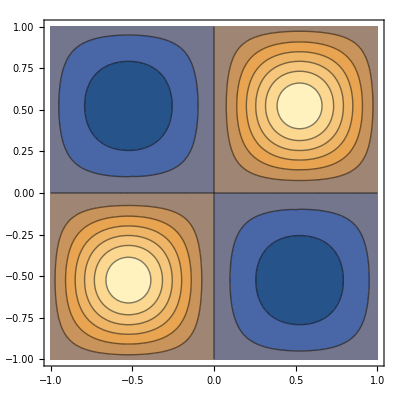

```mathematica
ContourPlot[qs0[[1]],{x,-1,1},{y,-1,1},PlotTheme->"Detailed",PlotLegends->Placed[BarLegend[Automatic],Above]]
```

```mathematica
Plot3D[qs0[[1]],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

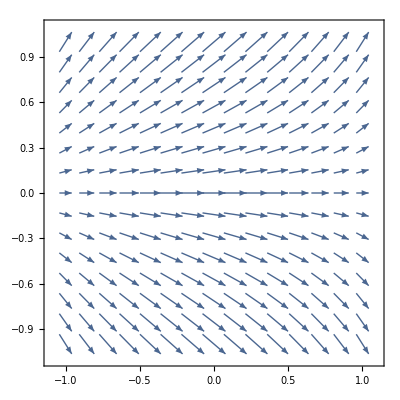

```mathematica
VectorPlot[{qs0[[2]],qs0[[3]]},{x,-1,1},{y,-1,1}]
```

```mathematica
CForm[%]
```

List(-Cos(t - x0) + Cos(3*t + x0) + Sin(4*t + y0),
   3*Cos(3*t + x0) + Cos(t - x0)*(7 - Sin(t - x0)) - 
    (2*Cos(3*t + x0)*(5 + Sin(3*t + x0)))/(-7 + Sin(t - x0)) - 
    (Cos(t - x0)*Power(5 + Sin(3*t + x0),2))/Power(-7 + Sin(t - x0),2) + 
    ((5 + Sin(3*t + x0))*Sin(4*t + y0))/(7 - Sin(t - x0)),
   (Cos(3*t + x0)*(3 + Cos(4*t + y0)))/(-7 + Sin(t - x0)) + 
    (Cos(t - x0)*(3 + Cos(4*t + y0))*(5 + Sin(3*t + x0)))/Power(-7 + Sin(t - x0),2) + 4*Sin(4*t + y0) + 
    (2*(3 + Cos(4*t + y0))*Sin(4*t + y0))/(-7 + Sin(t - x0)))

```mathematica
temp1=Simplify[D[qs[x,y,t],t]+D[F1[x,y,t],x]+D[F2[x,y,t],y]]
```

{-7+2 t-2 y,0,-1+(2 (t-y)^2)/(-4+t-y)^3+(2 (-t+y))/(4-t+y)^2+2 (4-t+y)^3}

```mathematica
CForm[temp1]
```

List(-7 + 2*t - 2*x,-1 + (2*Power(t - x,2))/Power(-4 + t - x,3) + 
    (2*(-t + x))/Power(4 - t + x,2) + 2*Power(4 - t + x,3),0)

```mathematica
Simplify[D[F1[x,y,t],x]+D[F2[x,y,t],y]]
```

{1,0,(2 (-4 t+4 y+(4-t+y)^6))/(4-t+y)^3}

```mathematica
F1[x,y,t]
```

{0,1/2 (4-t+y)^4,0}

## As for inout BC:

```mathematica
An1[q1_,q2_,q3_]:={{0,1,0},{-q2*q2/q1/q1+q1,2*q2/q1,0},{-q2*q3/q1/q1,q3/q1,q2/q1}}
```

```mathematica
An2[q1_,q2_,q3_]:={{0,0,1},{-q2*q3/q1/q1,q3/q1,q2/q1},{-q3*q3/q1/q1+q1,0,2*q3/q1}}
```

```mathematica
An2[q1,q2,q3]
```

{{0,0,1},{-(q2 q3)/q1^2,q3/q1,q2/q1},{q1-q3^2/q1^2,0,(2 q3)/q1}}

```mathematica
An[q1_,q2_,q3_,n1_,n2_]:=An1[q1,q2,q3]*n1+An2[q1,q2,q3]*n2
```

```mathematica
AnN=An[q1,q2,q3,n1,n2]
```

{{0,n1,n2},{n1 (q1-q2^2/q1^2)-(n2 q2 q3)/q1^2,(2 n1 q2)/q1+(n2 q3)/q1,(n2 q2)/q1},{-(n1 q2 q3)/q1^2+n2 (q1-q3^2/q1^2),(n1 q3)/q1,(n1 q2)/q1+(2 n2 q3)/q1}}

```mathematica
Λn[q1_,q2_,q3_,n1_,n2_]:=Simplify[DiagonalMatrix[Eigenvalues[AnN]],n1^2+n2^2==1&&{q1,q2,q3,n1,n2}∈Reals&&q1>0]
```

```mathematica
ΛnN=Λn[q1,q2,q3,n1,n2]
```

{{(n1 q2+n2 q3)/q1,0,0},{0,(-q1^(3/2)+n1 q2+n2 q3)/q1,0},{0,0,(q1^(3/2)+n1 q2+n2 q3)/q1}}

```mathematica
Vn[q1_,q2_,q3_,n1_,n2_]:=(n1 q2+n2 q3)/q1
VnN=Vn[q1,q2,q3,n1,n2]
```

(n1 q2+n2 q3)/q1

```mathematica
ΛnN={{VnN,0,0},{0,VnN-√q1,0},{0,0,VnN+√q1}}
```

{{(n1 q2+n2 q3)/q1,0,0},{0,-√q1+(n1 q2+n2 q3)/q1,0},{0,0,√q1+(n1 q2+n2 q3)/q1}}

```mathematica
Rn[q1_,q2_,q3_,n1_,n2_]:=Transpose[Simplify[Eigenvectors[An[q1,q2,q3,n1,n2]],n1^2+n2^2==1&&{q1,q2,q3,n1,n2}∈Reals&&q1>0]]
```

```mathematica
Rn[q1,q2,q3,n1,n2]
```

{{0,-q1/(n2 q1^(3/2)-q3),q1/(n2 q1^(3/2)+q3)},{-n2/n1,(n1 q1^(3/2)-q2)/(n2 q1^(3/2)-q3),(n1 q1^(3/2)+q2)/(n2 q1^(3/2)+q3)},{1,1,1}}

```mathematica
RnN=Simplify[{{0,-q1,q1},{-n2,n1 q1^(3/2)-q2,n1 q1^(3/2)+q2},{n1,n2 q1^(3/2)-q3,n2 q1^(3/2)+q3}}]
```

{{0,-q1,q1},{-n2,n1 q1^(3/2)-q2,n1 q1^(3/2)+q2},{n1,n2 q1^(3/2)-q3,n2 q1^(3/2)+q3}}

```mathematica
Ln[q1_,q2_,q3_,n1_,n2_]:=Simplify[Inverse[Rn[q1,q2,q3,n1,n2]],n1^2+n2^2==1&&{q1,q2,q3,n1,n2}∈Reals&&q1>0]
```

```mathematica
LnN=Simplify[Inverse[RnN],n1^2+n2^2==1&&{q1,q2,q3,n1,n2}∈Reals&&q1>0]
```

{{(n2 q2-n1 q3)/q1,-n2,n1},{(-q1^(3/2)-n1 q2-n2 q3)/(2 q1^(5/2)),n1/(2 q1^(3/2)),n2/(2 q1^(3/2))},{(q1^(3/2)-n1 q2-n2 q3)/(2 q1^(5/2)),n1/(2 q1^(3/2)),n2/(2 q1^(3/2))}}

```mathematica
Simplify[AnN-RnN.ΛnN.LnN,n1^2+n2^2==1&&{q1,q2,q3,n1,n2}∈Reals&&q1>0]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Simplify[D[ΛnN,q1],n1^2+n2^2==1&&{q1,q2,q3,n1,n2}∈Reals&&q1>0]
```

{{-(n1 q2+n2 q3)/q1^2,0,0},{0,-(q1^(3/2)+2 n1 q2+2 n2 q3)/(2 q1^2),0},{0,0,(q1^(3/2)-2 n1 q2-2 n2 q3)/(2 q1^2)}}

```mathematica
Simplify[D[ΛnN,q2],n1^2+n2^2==1&&{q1,q2,q3,n1,n2}∈Reals&&q1>0]
```

{{n1/q1,0,0},{0,n1/q1,0},{0,0,n1/q1}}

```mathematica
Simplify[D[ΛnN,q3],n1^2+n2^2==1&&{q1,q2,q3,n1,n2}∈Reals&&q1>0]
```

{{n2/q1,0,0},{0,n2/q1,0},{0,0,n2/q1}}

```mathematica
Simplify[D[RnN,q1],n1^2+n2^2==1&&{q1,q2,q3,n1,n2}∈Reals&&q1>0]
```

{{0,(n2 q1^(3/2)+2 q3)/(2 (-n2 q1^(3/2)+q3)^2),(-n2 q1^(3/2)+2 q3)/(2 (n2 q1^(3/2)+q3)^2)},{0,(3 √q1 (n2 q2-n1 q3))/(2 (-n2 q1^(3/2)+q3)^2),(3 √q1 (-n2 q2+n1 q3))/(2 (n2 q1^(3/2)+q3)^2)},{0,0,0}}

```mathematica
Simplify[D[RnN,q2],n1^2+n2^2==1&&{q1,q2,q3,n1,n2}∈Reals&&q1>0]
```

{{0,0,0},{0,1/(-n2 q1^(3/2)+q3),1/(n2 q1^(3/2)+q3)},{0,0,0}}

```mathematica
Simplify[D[RnN,q3],n1^2+n2^2==1&&{q1,q2,q3,n1,n2}∈Reals&&q1>0]
```

{{0,-q1/((-n2 q1^(3/2)+q3)^2),-q1/((n2 q1^(3/2)+q3)^2)},{0,(n1 q1^(3/2)-q2)/((-n2 q1^(3/2)+q3)^2),-(n1 q1^(3/2)+q2)/((n2 q1^(3/2)+q3)^2)},{0,0,0}}

```mathematica
Simplify[D[LnN,q1],n1^2+n2^2==1&&{q1,q2,q3,n1,n2}∈Reals&&q1>0]
```

{{(n1 (-n2 q2+n1 q3))/q1^2,0,0},{(2 n2^2 q1^(3/2) q3-(2 q1^(3/2)+5 n1 q2) q3-n2 (q1^3-2 n1 q1^(3/2) q2+5 q3^2))/(4 q1^(7/2)),(3 n1 q3)/(4 q1^(5/2)),(3 n2 q3)/(4 q1^(5/2))},{(-2 q1^(3/2) q3+2 n2^2 q1^(3/2) q3+5 n1 q2 q3+n2 (q1^3+2 n1 q1^(3/2) q2+5 q3^2))/(4 q1^(7/2)),-(3 n1 q3)/(4 q1^(5/2)),-(3 n2 q3)/(4 q1^(5/2))}}

```mathematica
Simplify[D[LnN,q2],n1^2+n2^2==1&&{q1,q2,q3,n1,n2}∈Reals&&q1>0]
```

{{(n1 n2)/q1,0,0},{(n1 (-n2 q1^(3/2)+q3))/(2 q1^(5/2)),0,0},{-(n1 (n2 q1^(3/2)+q3))/(2 q1^(5/2)),0,0}}

```mathematica
Simplify[D[LnN,q3],n1^2+n2^2==1&&{q1,q2,q3,n1,n2}∈Reals&&q1>0]
```

{{-n1^2/q1,0,0},{(-(-1+n2^2) q1^(3/2)+n1 q2+2 n2 q3)/(2 q1^(5/2)),-n1/(2 q1^(3/2)),-n2/(2 q1^(3/2))},{(-(-1+n2^2) q1^(3/2)-n1 q2-2 n2 q3)/(2 q1^(5/2)),n1/(2 q1^(3/2)),n2/(2 q1^(3/2))}}

#### The first case: 0<√h≤V_n

```mathematica
absΛn[q1_,q2_,q3_,n1_,n2_]:={{VnN,0,0},{0,VnN-√q1,0},{0,0,VnN+√q1}}
```

```mathematica
absΛnN=Simplify[absΛn[q1,q2,q3,n1,n2],n1^2+n2^2==1&&{q1,q2,q3,n1,n2}∈Reals&&q1>0]
```

{{(n1 q2+n2 q3)/q1,0,0},{0,(-q1^(3/2)+n1 q2+n2 q3)/q1,0},{0,0,(q1^(3/2)+n1 q2+n2 q3)/q1}}

```mathematica
Simplify[D[absΛnN,q1],n1^2+n2^2==1&&{q1,q2,q3,n1,n2}∈Reals&&q1>0]
```

{{-(n1 q2+n2 q3)/q1^2,0,0},{0,-(q1^(3/2)+2 n1 q2+2 n2 q3)/(2 q1^2),0},{0,0,(q1^(3/2)-2 n1 q2-2 n2 q3)/(2 q1^2)}}

```mathematica
Simplify[D[absΛnN,q2],n1^2+n2^2==1&&{q1,q2,q3,n1,n2}∈Reals&&q1>0]
```

{{n1/q1,0,0},{0,n1/q1,0},{0,0,n1/q1}}

```mathematica
Simplify[D[absΛnN,q3],n1^2+n2^2==1&&{q1,q2,q3,n1,n2}∈Reals&&q1>0]
```

{{n2/q1,0,0},{0,n2/q1,0},{0,0,n2/q1}}

#### The second case: 0≤V_n<√h

```mathematica
absΛn[q1_,q2_,q3_,n1_,n2_]:={{VnN,0,0},{0,-VnN+√q1,0},{0,0,VnN+√q1}}
```

```mathematica
absΛnN=absΛn[q1,q2,q3,n1,n2]
```

{{(n1 q2+n2 q3)/q1,0,0},{0,√q1-(n1 q2+n2 q3)/q1,0},{0,0,√q1+(n1 q2+n2 q3)/q1}}

```mathematica
plsΛnN={{VnN,0,0},{0,0,0},{0,0,VnN+√q1}}
```

{{(n1 q2+n2 q3)/q1,0,0},{0,0,0},{0,0,√q1+(n1 q2+n2 q3)/q1}}

```mathematica
mnsΛnN={{0,0,0},{0,Vn-√q1,0},{0,0,0}}
```

{{0,0,0},{0,-√q1+Vn,0},{0,0,0}}

```mathematica
absAnN=Simplify[RnN.absΛnN.LnN,n1^2+n2^2==1&&{q1,q2,q3,n1,n2}∈Reals&&q1>0]
```

{{((q1^(3/2)-n1 q2-n2 q3) (q1^(3/2)+n1 q2+n2 q3))/q1^(5/2),(n1 (n1 q2+n2 q3))/q1^(3/2),(n2 (n1 q2+n2 q3))/q1^(3/2)},{(q1^3 q2+q2 ((-1+n2^2) q2^2-2 n1 n2 q2 q3-n2^2 q3^2)+n2 q1^(3/2) ((1-2 n2^2) q2 q3+n1 n2 (-q2^2+q3^2)))/q1^(7/2),(n1^2 (q1^3+q2^2)+n2^3 q1^(3/2) q3+n1 n2 q2 (n2 q1^(3/2)+q3))/q1^(5/2),(n2 (n1^2 (q1^3+q2^2)+n2 (-1+n2^2) q1^(3/2) q3+n1 q2 ((-1+n2^2) q1^(3/2)+n2 q3)))/(n1 q1^(5/2))},{(-n1^3 q1^(3/2) q2 q3+n1 n2 q2 (n2 q1^(3/2)-2 q3) q3+q3 (q1^3-n2^2 q3^2)+n1^2 (-q2^2 q3+n2 q1^(3/2) (q2^2-q3^2)))/q1^(7/2),-(n1 (n2^2 q1^(3/2) q3-n1 q2 q3-n2 (q1^3-n1 q1^(3/2) q2+q3^2)))/q1^(5/2),(n1 q1^(3/2) q2-n2^3 q1^(3/2) q3+n2 (q1^(3/2)+n1 q2) q3+n2^2 (q1^3-n1 q1^(3/2) q2+q3^2))/q1^(5/2)}}

```mathematica
Simplify[D[absAnN,q1],n1^2+n2^2==1&&{q1,q2,q3,n1,n2}∈Reals&&q1>0]
```

{{(q1^3+5 (n1 q2+n2 q3)^2)/(2 q1^(7/2)),-(3 n1 (n1 q2+n2 q3))/(2 q1^(5/2)),-(3 n2 (n1 q2+n2 q3))/(2 q1^(5/2))},{(-q1^3 q2+4 n2 q1^(3/2) ((-1+2 n2^2) q2 q3+n1 n2 (q2^2-q3^2))+7 (q2^3+2 n1 n2 q2^2 q3+n2^2 (-q2^3+q2 q3^2)))/(2 q1^(9/2)),(n1^2 (q1^3-5 q2^2)-2 n2^3 q1^(3/2) q3-n1 n2 q2 (2 n2 q1^(3/2)+5 q3))/(2 q1^(7/2)),(n2 (n1^2 (q1^3-5 q2^2)-2 n2 (-1+n2^2) q1^(3/2) q3+n1 q2 (-2 (-1+n2^2) q1^(3/2)-5 n2 q3)))/(2 n1 q1^(7/2))},{(-q1^3 q3+4 n1^3 q1^(3/2) q2 q3+7 n2^2 q3^3+2 n1 n2 q2 q3 (-2 n2 q1^(3/2)+7 q3)+n1^2 (7 q2^2 q3+4 n2 q1^(3/2) (-q2^2+q3^2)))/(2 q1^(9/2)),(n1 (2 n2^2 q1^(3/2) q3-5 n1 q2 q3+n2 (q1^3+2 n1 q1^(3/2) q2-5 q3^2)))/(2 q1^(7/2)),(-2 n1 q1^(3/2) q2+2 n2^3 q1^(3/2) q3-n2 (2 q1^(3/2)+5 n1 q2) q3+n2^2 (q1^3+2 n1 q1^(3/2) q2-5 q3^2))/(2 q1^(7/2))}}

```mathematica
plsAnN=Simplify[RnN.plsΛnN.LnN,n1^2+n2^2==1&&{q1,q2,q3,n1,n2}∈Reals&&q1>0]
```

{{((q1^(3/2)-n1 q2-n2 q3) (q1^(3/2)+n1 q2+n2 q3))/(2 q1^(5/2)),(n1 (q1^(3/2)+n1 q2+n2 q3))/(2 q1^(3/2)),(n2 (q1^(3/2)+n1 q2+n2 q3))/(2 q1^(3/2))},{-(n2 (n2 q2-n1 q3) (n1 q2+n2 q3))/q1^2+((n1 q1^(3/2)+q2) (q1^(3/2)-n1 q2-n2 q3) (q1^(3/2)+n1 q2+n2 q3))/(2 q1^(7/2)),(-(-1+n2^2) q1^3+q2 (q2-n2^2 q2+n1 n2 q3)+q1^(3/2) (n1 (2+n2^2) q2+n2 (1+n2^2) q3))/(2 q1^(5/2)),(n2 (-(-1+n2^2) q1^3+q2 (q2-n2^2 q2+n1 n2 q3)+n2 q1^(3/2) (n1 n2 q2+(-1+n2^2) q3)))/(2 n1 q1^(5/2))},{(n1 (n2 q2-n1 q3) (n1 q2+n2 q3))/q1^2+((n2 q1^(3/2)+q3) (q1^(3/2)-n1 q2-n2 q3) (q1^(3/2)+n1 q2+n2 q3))/(2 q1^(7/2)),-(n1 n2 (n1 q2+n2 q3))/q1+(n1 (n2 q1^(3/2)+q3) (q1^(3/2)+n1 q2+n2 q3))/(2 q1^(5/2)),-((-1+n2^2) (n1 q2+n2 q3))/q1+(n2 (n2 q1^(3/2)+q3) (q1^(3/2)+n1 q2+n2 q3))/(2 q1^(5/2))}}

```mathematica
Simplify[D[plsAnN,q1],n1^2+n2^2==1&&{q1,q2,q3,n1,n2}∈Reals&&q1>0]
```

{{(q1^3+5 (n1 q2+n2 q3)^2)/(4 q1^(7/2)),-(3 n1 (n1 q2+n2 q3))/(4 q1^(5/2)),-(3 n2 (n1 q2+n2 q3))/(4 q1^(5/2))},{(-q1^3 q2+7 q2^3+8 n2^3 q1^(3/2) q2 q3+n2^2 (-7 q2^3+7 q2 q3^2)+2 n1 (q1^(9/2)+7 n2 q2^2 q3+2 q1^(3/2) (q2^2+n2^2 (q2^2-q3^2))))/(4 q1^(9/2)),(-(-1+n2^2) q1^3-5 q2 (q2-n2^2 q2+n1 n2 q3)-2 q1^(3/2) (n1 (2+n2^2) q2+n2 (1+n2^2) q3))/(4 q1^(7/2)),(n2 (-(-1+n2^2) q1^3-5 q2 (q2-n2^2 q2+n1 n2 q3)-2 n2 q1^(3/2) (n1 n2 q2+(-1+n2^2) q3)))/(4 n1 q1^(7/2))},{1/(4 q1^(9/2))((-q1^3+8 n1^3 q1^(3/2) q2+7 n1^2 q2^2) q3+4 n2^3 q1^(3/2) q3^2+7 n2^2 q3^3+2 n2 (q1^(9/2)+7 n1 q2 q3^2+2 (-1+n2^2) q1^(3/2) (q2^2-2 q3^2))),(n1 (2 n2^2 q1^(3/2) q3-(2 q1^(3/2)+5 n1 q2) q3+n2 (q1^3+2 n1 q1^(3/2) q2-5 q3^2)))/(4 q1^(7/2)),(-4 n1 q1^(3/2) q2+2 n2^3 q1^(3/2) q3-n2 (6 q1^(3/2)+5 n1 q2) q3+n2^2 (q1^3+2 n1 q1^(3/2) q2-5 q3^2))/(4 q1^(7/2))}}

```mathematica
mnsAnN=Simplify[RnN.mnsΛnN.LnN,n1^2+n2^2==1&&{q1,q2,q3,n1,n2}∈Reals&&q1>0]
```

{{((q1^(3/2)+n1 q2+n2 q3) (-√q1+Vn))/(2 q1^(3/2)),1/2 (n1-(n1 Vn)/(√q1)),1/2 (n2-(n2 Vn)/(√q1))},{((n1 q1^(3/2)-q2) (q1^(3/2)+n1 q2+n2 q3) (√q1-Vn))/(2 q1^(5/2)),-(n1 (n1 q1^(3/2)-q2) (√q1-Vn))/(2 q1^(3/2)),-(n2 (n1 q1^(3/2)-q2) (√q1-Vn))/(2 q1^(3/2))},{((n2 q1^(3/2)-q3) (q1^(3/2)+n1 q2+n2 q3) (√q1-Vn))/(2 q1^(5/2)),1/2 n1 (n2-q3/q1^(3/2)) (-√q1+Vn),1/2 n2 (n2-q3/q1^(3/2)) (-√q1+Vn)}}

#### The third case: -√h≤V_n<0

#### The fourth case: V_n<-√h<0

{t y Cos[t x y]+ⅇ^(t (x+y)) Cos[t+x+y]-t x Sin[t x y]+ⅇ^(t (x+y)) (x+y) Sin[t+x+y],x y Cos[t x y]+(t x Cos[t x y]^2)/(10+ⅇ^(t (x+y)) Sin[t+x+y])-(t x Sin[t x y]^2)/(10+ⅇ^(t (x+y)) Sin[t+x+y])+(t y Sin[2 t x y])/(10+ⅇ^(t (x+y)) Sin[t+x+y])-(ⅇ^(t (x+y)) Sin[t x y]^2 (Cos[t+x+y]+t Sin[t+x+y]))/((10+ⅇ^(t (x+y)) Sin[t+x+y])^2)-(ⅇ^(t (x+y)) Sin[2 t x y] (Cos[t+x+y]+t Sin[t+x+y]))/(2 (10+ⅇ^(t (x+y)) Sin[t+x+y])^2)+ⅇ^(t (x+y)) (10+ⅇ^(t (x+y)) Sin[t+x+y]) (Cos[t+x+y]+t Sin[t+x+y]),-x y Sin[t x y]+(t y Cos[t x y]^2)/(10+ⅇ^(t (x+y)) Sin[t+x+y])-(t y Sin[t x y]^2)/(10+ⅇ^(t (x+y)) Sin[t+x+y])-(t x Sin[2 t x y])/(10+ⅇ^(t (x+y)) Sin[t+x+y])-(ⅇ^(t (x+y)) Cos[t x y]^2 (Cos[t+x+y]+t Sin[t+x+y]))/((10+ⅇ^(t (x+y)) Sin[t+x+y])^2)-(ⅇ^(t (x+y)) Sin[2 t x y] (Cos[t+x+y]+t Sin[t+x+y]))/(2 (10+ⅇ^(t (x+y)) Sin[t+x+y])^2)+ⅇ^(t (x+y)) (10+ⅇ^(t (x+y)) Sin[t+x+y]) (Cos[t+x+y]+t Sin[t+x+y])}